# Spatial Hypergraph Growth Rate Filtering

Example on how to use the wolframLinearFilter, wolframModelGenConnect, and wolframExponentialFilter to find models constructed from a large set of rules which exhibit non-linear and non-exponential scaling growth rates (non-linear and non-exponential as the filters define them for now - some models with growth rates which are somewhat linear or exponential still pass).

NOTE: Before any of the custom functions may be used in this notebook, the WM_GrowthRate_Funcs.nb must be evaluated so they are in the initialized within the current kernel.

### Importing/Initialization of Rules

Two ways in which a set of rules can be constructed - RandomWolframModel and EnumerateWolframModelRules. The rules used below for example are generated from the enumeration of the signature 1_3→2_3, which are imported in as a wxf file which Stephen supplied (he has enumerated over a lot of signatures already, as enumerating over high arity and complex signatures requires too large computational power for the standard, personal laptop).

A simple example of how to use the functions:

Importing 1_3→2_3 rules:

```mathematica
SetDirectory[NotebookDirectory[]];
rulelist = Import["Archive\\12-22c.wxf"];
Length[rulelist]
```

73

Splitting list into a set of sublists:

```mathematica
rulesublists = Partition[rulelist,20];
Length[rulesublists]
```

3

Splitting list into a set of sublists:

```mathematica
sublisttesting =Timing[wolframFilterTest1[rulesublists,1,Length[rulesublists],1]]
```

{16.5625,{Non-Valid,Non-Valid,Non-Valid}}

For any sublist which is marked “Valid” (meaning a model within the sublist passes the wolframExoticGrowthFilter), can then specifically call on it from within rulesublists to re-run through the filters and see which specific model passes

Testing the first sublist in the set:

```mathematica
ruletesting = rulesublists[[1]];
```

Generating list of models associated to each rule:

```mathematica
modeltesting = modelGenerator[ruletesting];
```

Running through the wolframExoticGrowthFilter, and then individually each of the filters just to check which model passes which filter. If wolframExoticGrowthFilter returns a empty list, nothing passed. If it returns a list of numbers, the numbers associated to the position of the model in the modeltesting list which passed the wolframExoticGrowthFilter:

```mathematica
wolframExoticGrowthfilter[modeltesting]
```

{}

```mathematica
wolframModelGenConnect[modeltesting]
```

{Passes,Passes,Passes,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass,Passes,Passes,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass,Passes,Passes,Passes,Passes,Passes}

```mathematica
wolframModelLinearFilter[modeltesting]
```

{Does Not Pass,Does Not Pass,Does Not Pass,Passes,Passes,Passes,Passes,Passes,Passes,Does Not Pass,Does Not Pass,Passes,Passes,Passes,Passes,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass}

```mathematica
wolframModelExponentialFilter[modeltesting]
```

{Does Not Pass,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Passes,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass,Does Not Pass}

Visualizing any model of interest :

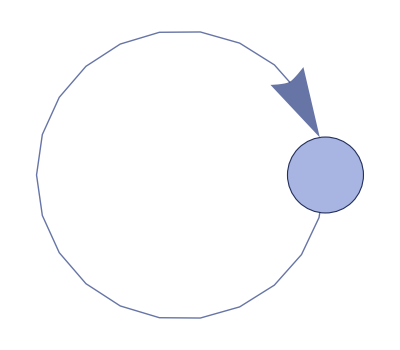
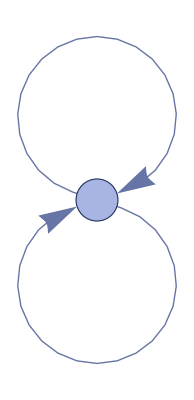
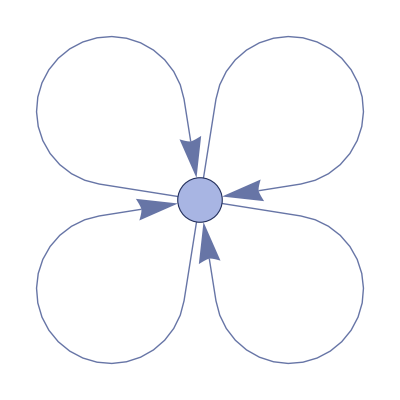
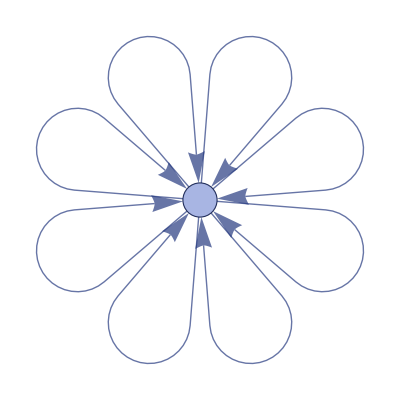
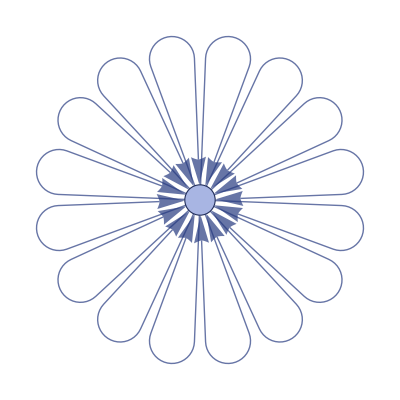
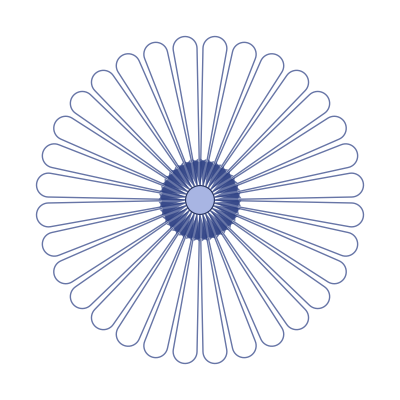
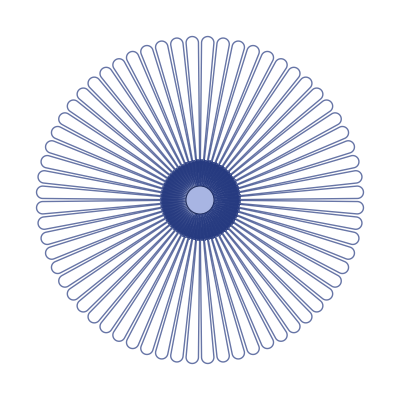
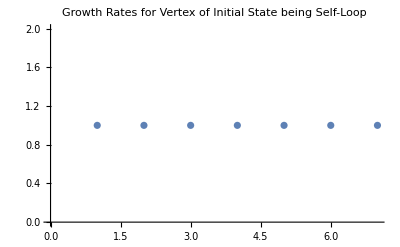
{{{{1,1}}→{{1,1},{1,1}}},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1,1,1,1,1,1,1},{1,2,4,8,16,32,64},-Graphics-,-Graphics-}

```mathematica
val =1;
wolframModelObjectProperties[modeltesting[[val]]]
```